## About LensFlow

Developer: Milad Pourrahmani (Miladiouss)
Email: mpourrah@uci.edu
Submission Date to GitHub: Jan. 30, 2018

### Publication

For detailed description of this project please refer to the following paper:
Title: LensFlow: A Convolutional Neural Network in Search of Strong Gravitational Lenses
Authors: Milad Pourrahmani, Hooshang Nayyeri, Asantha Cooray
Institution: Cooray Group at Department of Physics and Astronomy at University of California, Irvine
Publication: Submitted to ApJ and ArXive on May 16th, 2017
ArXive Link: https://arxiv.org/abs/1705.05857
Abstract: In this work, we present our machine learning classification algorithm for identifying strong gravitational lenses from wide-area surveys using convolutional neural networks; LensFlow. We train and test the algorithm using a wide variety of strong gravitational lens configurations from simulations of lensing events. Images are processed through multiple convolutional layers which extract feature maps necessary to assign a lens probability to each image. LensFlow, provides a ranking scheme for all sources which could be used to identify potential gravitational lens candidates by significantly reducing the number of images that have to be visually inspected. We apply our algorithm to the HST/ACS i-band observations of the COSMOS field and present our sample of identified lensing candidates. The developed machine learning algorithm is more computationally efficient and complimentary to classical lens identification algorithms and is ideal for discovering such events across wide areas from current and future surveys such as LSST and WFIRST.

### About this notebook and other materials in this repository

As stated in the abstract about, this project was created to demonstrate the usefulness of convolutional neural networks (CNNs) in the field of observational cosmology and astrophysics. In particular, we wanted to show that CNNs are capable of identifying previously knows lenses in the COSMOS field which was captured by Hubble Space Telescope and was released back in 2007. The techniques developed here are not limited to lens identification and can be used to classify galaxies based on their morphologies as well. 
The code provided in this notebook was developed in Mathematica 11.3 (on Ubuntu 17.10) and has been slightly modified from the version used for publication but it does contain all the main features. This notebook requires a GPU. If you do not have access to one, please see “GPU Information” section to let the Mathematica know to use your CPU instead. 
This notebook does not contain the procedure to download, to source extract, to crop, and to normalize COSMOS images. It also doesn’t contain the lens simulation pipeline. Having said that, I have included the Jupyter notebook (called “Handy COSMOS ACS Functions.ipynb”)that I have used for all these purposes, but it is not well organized and well documented. However, all functions have a doc string and all variables are fully spelled out for transparency. If you are just getting started in observational astrophysics, I think you might find many of those function helpful. For instance, you can find code for automating image cropping from multiple and large FTIS files using astropy, or learn how to automatically run SourceExtractor on multiple files and much more. I also did a lot of personal experimentations towards the end that should be commented out but be careful and avoid running the entire notebook at once.

## Definition of Helper Functions, Quantities, and Directories

### GPU Information

We would like to thank NVIDIA for donating a Titan Xp GPU to our research group which we deployed using an external GPU enclosure made by Mantiz. If you have an internal or external GPU, make sure Mathematica can recognize it. You can do so by running the following cells and see if your GPU is listed.

Navigate to `Links` and then to `CUDA`.

```mathematica
Needs["CUDALink`"]
SystemInformation[]
```

1234567

You must run the following so the NetTrain would know to use GPUs instead of CPUs. If you don’t have a GPU, simply change “GPU” to “CPU”

```mathematica
targetDevice="GPU";
```

### Dataset structure and sample data

In this project, the term dataset (in a machine learning context, not to be confused with “Dataset” from Mathematica) refers to a list of associated images to their corresponding class. These images must be normalized (see Image normalization via a template histogram). Training and testing datasets can be created using datasetMaker. When I was using this notebook, I would load the entire cutouts from the COSMSOS field into a variable called cosmos which contains 81 lists associated to the name of the tile those images came from. This is not possible if the cutouts are saved as FITS since it is not compressed and these they must be stored as JPEG to become more manageable. The lists inside cosmos, furthermore, consist of {image, "filename", "label"} elements, sometimes a few thousands of them. The following is a shortened version of the variable cosmos. (I do admit it would have been better if I used the Mathematica “Dataset” to handle this).

```mathematica
cosmos={
"tile1"->{{-Graphics-,"enh_cosmos_acs_t078_i1009_x7981_y4118.jpeg","unclassified"},{-Graphics-,"enh_cosmos_acs_t078_i1011_x8965_y4121.jpeg","unclassified"},{-Graphics-,"enh_cosmos_acs_t078_i1012_x10426_y4236.jpeg","unclassified"},{-Graphics-,"enh_cosmos_acs_t078_i1013_x9126_y4178.jpeg","unclassified"}},

"tile2"->{{-Graphics-,"enh_cosmos_acs_t079_i1008_x19009_y4250.jpeg","unclassified"},{-Graphics-,"enh_cosmos_acs_t079_i1009_x12698_y4277.jpeg","unclassified"},{-Graphics-,"enh_cosmos_acs_t079_i1012_x1159_y4314.jpeg","unclassified"}}
};
```

The following contains a few examples of simulated lenes:

```mathematica
simulatedLenses={-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

#### Tracer Lenses

The following lists contain a few of examples from the discovered lenses by Faure et. al. These images are used as tracer data to measure the performance of our classifier in Phase 1 and Phase 2.

```mathematica
tracerLenses={{-Graphics-,"Lens 1","Faure Lens"},{-Graphics-,"Lens 2","Faure Lens"},{-Graphics-,"Lens 3","Faure Lens"},{-Graphics-,"Lens 4","Faure Lens"},{-Graphics-,"Lens 5","Faure Lens"},{-Graphics-,"Lens 6","Faure Lens"},{-Graphics-,"Lens 7","Faure Lens"},{-Graphics-,"Lens 8","Faure Lens"},{-Graphics-,"Lens 9","Faure Lens"},{-Graphics-,"Lens 11","Faure Lens"},{-Graphics-,"Lens 12","Faure Lens"},{-Graphics-,"Lens 16","Faure Lens"},{-Graphics-,"Lens 17","Faure Lens"},{-Graphics-,"Lens 18","Faure Lens"}};
```

### Image normalization via a template histogram

Image normalization is an important step for preparing data for CNNs. Often, for daily objects or handwritten digits, programmers simply bound the pixel values and transform the mean or the standard deviation. This method did not work on our images since pixel due to a wider pixel range and abundance of noise in astronomical data. Instead, we use histogram transformation. Not only this method bounds the pixel values, but also insures similar statistical moments among all images. To obtain a template histogram, I have selected one of the dimmest lenses and have adjusted its brightness, contrast, and performed gamma correction on it until its arc became clearly visible. The following captures the template histogram.

```mathematica
templateHistogram=HistogramDistribution@ImageAdjust[-Graphics-,{1.,.5,.3}];
```

I have defined the following normalizing function that takes a datasets (i.e. a list of images and their associated labels)  which converts images to the correct size, then to grayscale, and then transforms their image histograms. See the following example.

```mathematica
normalizeDataset[dataset_,imageSize_,templateHistogram_]:=Module[{adjustedData=dataset},
adjustedData[[All,1]]=ImageResize[#,imageSize]&/@adjustedData[[All,1]];
adjustedData[[All,1]]=ColorConvert[#,"Grayscale"]&/@adjustedData[[All,1]];
adjustedData[[All,1]]=HistogramTransform[#,templateHistogram]&/@adjustedData[[All,1]];
adjustedData]
```

```mathematica
normalizeDataset[{-Graphics-->"airplane",-Graphics-->"non-lens"},100{1,1},templateHistogram]
```

{-Graphics-→airplane,-Graphics-→non-lens}

### Dataset Maker

datasetMaker will take the following listed of arguments and return a training and a testing dataset ({trainingDataset, testDataset}). See the commented example bellow after defining the function.

List of arguments:
1. list of images of one class (e.g. {img1, img2})
2. corresponding class name: (e.g. “non-lens”)
3. number of images separated as test data: (e.g. 0)
4. number of augmentations: (e.g. 8)
5. augmentation (crop/trim) size relative to the imageSize: (e.g. 100{1,1})
6. apply rotation: True/False
7. final image size: imageSize

```mathematica
(*dataMaker[{-Graphics-,-Graphics-,-Graphics-,-Graphics-},"lens",1,0,100 {1,1},True,100 {1,1}]*)
```

```mathematica
datasetMaker[images_,class_,testSize_,augment_,augmentCropSize_,rotate_,finalImageSize_]:=Module[{trainingData={},testData={},shuffledImages,augmenter,imageRotator,trainingImages,testImages,subset,c},

imageRotator[img_]:={
img,
ImageRotate[img,90°],
ImageRotate[img,180°],
ImageRotate[img,270°],
ImageReflect[img,Top->Bottom],
ImageReflect[img,Left->Right],
ImageReflect[img,Left->Top],
ImageReflect[img,Right->Top]
};


SeedRandom[1234];
shuffledImages=RandomSample@images;

trainingImages=shuffledImages[[1;;Length[shuffledImages]-testSize]];

If[augment≠0,augmenter=ImageAugmentationLayer[Ceiling[augmentCropSize],"ReflectionProbabilities"->{0,0},"Input"->NetEncoder[{"Image",finalImageSize}],"Output"->NetDecoder["Image"]];];
trainingImages=Flatten@If[augment≠0,Table[augmenter[#,NetEvaluationMode->"Train"]&/@trainingImages,{i,augment}],trainingImages];
trainingImages=ImageResize[#,finalImageSize]&/@trainingImages;
trainingImages=Flatten@If[rotate==True,imageRotator/@trainingImages,trainingImages];
trainingImages=ColorConvert[#,"Grayscale"]&/@trainingImages;
trainingData=#->class&/@trainingImages;


testImages=shuffledImages[[1+Length[shuffledImages]-testSize;;Length[shuffledImages]]];

testImages=Flatten@If[augment≠0,Table[augmenter[#,NetEvaluationMode->"Train"]&/@testImages,{i,augment}],testImages];
testImages=ImageResize[#,finalImageSize]&/@testImages;
testImages=Flatten@If[rotate==True,imageRotator/@testImages,testImages];
testData=#->class&/@testImages;

{trainingData,testData}
]
```

### Scan

scan will take a list called imageNameClassList (see knownLenses as an example).

```mathematica
scan[imageNameClassList_,trainedNet_]:=Module[{data,getLensProbNet,scanningResults,netImageSize=(Normal@NetExtract[trainedNet,"Input"])["ImageSize"]},
SeedRandom[1234];
data=RandomSample[imageNameClassList];
data[[All,1]]=ImageResize[#,netImageSize]&/@data[[All,1]];
getLensProbNet=NetChain[trainedNet[[All]],"Input"->NetEncoder[{"Image",ColorSpace->"Grayscale",netImageSize}]];
scanningResults={data[[All,1]],data[[All,2]],getLensProbNet[data[[All,1]],TargetDevice->targetDevice]}ᵀ;
scanningResults
]
```

### Sort

sort will sort the scan results() based on the assigned probability for a given class (sortByClassesList, e.g. {“spiral”}) . If a list of class names (sortByClassesList, e.g. {“star”, “spiral”}) is provided, the sorting will be based on the sum of the probability for those two classes. A list of all classes must be provided.

```mathematica
sort[scanResults_,sortByClassesList_,classes_]:=Module[{sortedResults},
sortedResults=Sort[scanResults,
Sum[#1⟦-1,FirstPosition[classes,cls]⟦1⟧⟧,{cls,sortByClassesList}]>=Sum[#2⟦-1,FirstPosition[classes,cls]⟦1⟧⟧,{cls,sortByClassesList}]&];
sortedResults
]
```

#### Rank locator

rankLocator takes a list of desired classes (classList, e.g. {“star”, “spiral”}) and specified minimum probabilities (minProbabilities, e.g. {0.1, 0.2}) and finds the first occurrence of the sum of those probabilities drop below the sum of minimum probabilities in the sortedResults. sortedResults must have the same format as knownLenses and full list of classes must be provided as well.

```mathematica
rankLocator[classList_,minProbabilities_,sortedResults_,classes_]:=FirstPosition[sortedResultsᵀ[[-1]],probabilities_/;Length[probabilities]==Length[classes]∧Sum[probabilities⟦FirstPosition[classes,cls]⟦1⟧⟧,{cls,classList}]≤ Total[minProbabilities]]//Flatten
```

#### Search dataset by name

This will be handy if you are looking for a file name in a list that has elements with the {image, fileName, class} format.

```mathematica
getByFileNames[fileNames_,imageNameClassList_]:=Cases[imageNameClassList,x_/;MemberQ[fileNames,x[[2]]]]
```

```mathematica
(*weighter[img_]:=Module[{imgDim=128{1,1},W=16,f},
f[r_,W_]:=1-N[ PDF[NormalDistribution[0,W],r]]/N[ PDF[NormalDistribution[0,W],0]];
HistogramTransform[ImageApplyIndexed[#1f[Norm[#2-ImageDimensions[-Graphics-]/2],W]&,img],templateHistogram]
]*)
```

#### Countdown

May be used as progress bar.

```mathematica
countDown[seconds_]:=Dynamic[#-Clock[{0,#,1},#,1]]&@seconds
```

#### Performance Measures

After training a CNN, we use them to assign a probability of belonging to a class to each input image. This is in contrast to labeling images with class names. Later, these probabilities are used for ranking images from highest probability to lowest probability in a given class. We define relative rank as the absolute rank of an image normalized by (i.e. divided by) the total number of the images. Hence, a simple way to capture the efficiency of a classifier is to place a handful of tracers from one class (e.g. “lens”) and measure their average relative ranks. To make it more meaningful, we have defined the following function so an classification efficiency of 1, 0, -1 would mean perfect classification, no classification, reverse classification respectively.

```mathematica
efficiency[relativeTracerRanks_]:=Module[{},2Mean[1-relativeTracerRanks]-1//N]
```

A more sophisticated way is to plot a “tracer rank curve(TRC)” as we have defined it in our paper (please refer to the paper and see Figure 8). Using this plot, we can compute the “ranking performance” defined as the area between the black TRC and the dashed red line of no discrimination divided by the area between a perfect TRC and the line of no discrimination (approximately 1/2 for large datasets).  The following functions will generate a TRC plot and calculate the ranking performance. See Plots > Ranks > Plot Ranks for concrete examples.

```mathematica
rankingPerformance[relativeTracerRanks_]:=2.(1./2.-Integrate[Interpolation[Table[{i/Length[#],#[[i]]},{i,Length[#]}]&@relativeTracerRanks][x],{x,0,1}])
```

```mathematica
rankPlot[relativeRanks_]:=ListPlot[
{Table[{100#[[i]],100 i/Length[#]},{i,Length[#]}]&@relativeRanks~Join~{{100,100}},Table[{i,i},{i,0,100,1}]},

PlotRange->{All,All},
Joined->{False,True},
PlotStyle->{Directive[Black,Thick],Directive[Red,Thin,Dashed]},

PlotLegends->Placed[{"Tracer Lenses","Line of no discrimination"},{Scaled[{0.35,0.2}], {0, 0.5}}],
Frame->True,
FrameLabel->{"Rank (%)","Number of Recovered Lenses (%)"},
FrameStyle->Directive[Black,12]]
```

#### Grid View

view takes a dataset, a starting point in that dataset, and displays a portion of the dataset as numRows×numClms grid. This is very useful for visually examining a sorted dataset.

```mathematica
view[data_,start_,numRows_,numClms_]:=Grid@Module[{images=data[[start;;start+numRows numClms-1]][[All,1]]},Table[Grid@{{images[[(r-1)numClms+c]]},{start-1+(r-1)numClms+c}},{r,numRows},{c,numClms}]]
```

#### Sexagesimal to Degree Convertor

Convert RA and Dec (separately) from hr/deg:min:sec to degrees with a specified number of digits on the right hand side of the decimal.

```mathematica
SexagesimalToDegree[{hrORdeg_,min_,sec_},coord_/;(coord=="RA"∨coord=="Dec"),numRHSdigits_:6]:=

Which[
coord=="RA",PaddedForm[(1/1 hrORdeg+1/60 min+1/3600 sec)360./24.,{Infinity,numRHSdigits},NumberPadding->{"", "0"},NumberSigns->{"-", "+"}],
coord=="Dec",PaddedForm[(1/1 hrORdeg+1/60 min+1/3600 sec)1./1.,{Infinity,numRHSdigits},NumberPadding->{"", "0"},NumberSigns->{"-", "+"}]
]
```

### Architecture of the Convolutional Neural Network

The following architecture is used for all phases and is captured in the following diagram:

-Graphics-

```mathematica
imageSize=100{1,1};
convolutionKernelSize=5;
nonlinearity=Tanh;

architecture=
{ConvolutionLayer[30,convolutionKernelSize],
nonlinearity,
PoolingLayer[2,2],

ConvolutionLayer[60,convolutionKernelSize],
nonlinearity,
PoolingLayer[2,2],

ConvolutionLayer[90,convolutionKernelSize],
nonlinearity,
PoolingLayer[2,2],

FlattenLayer[],

1000,
Ramp,
DropoutLayer[0.5],

800,
Ramp,
DropoutLayer[0.5],

600,
Ramp,
DropoutLayer[0.5]};
```

## Pretraining Phase (Phase 0)

Since generating simulated lenses is expensive, our dataset might be very small. To overcome this challenge, we will use “transfer learning” by training our CNN on two classes of CIFAR-10.

### Importing airplanes and automobiles from CIFAR-10

```mathematica
CIFAR10Object=ResourceObject["CIFAR-10"];
trainingDataCIFAR2=ResourceData[CIFAR10Object,"TrainingData1"]; (* This only contains airplanes and automobiles *)
testDataCIFAR2=ResourceData[CIFAR10Object,"TestData"][[1;;1000 2]];
```

### Image Normalization

Convert all images to grayscale, resize them to `imageSize` and transform the image so it would match `templateHistogram`. This will take about 170 seconds.

```mathematica
normalizedTrainingDataCIFAR2=normalizeDataset[trainingDataCIFAR2,imageSize, templateHistogram];
normalizedTestDataCIFAR2=normalizeDataset[testDataCIFAR2,imageSize, templateHistogram];
```

You must save all variables and restart the notebook since NetTrain is a little unstable. I assume, this is due to memory issues. To save all variables:

```mathematica
If[False, DumpSave["/home/USER/Desktop/saved_Mathematica_stuff.mx","Global`"]]
```

After setting up the correct directory, this is how you would load it:

```mathematica
<<"/home/USER/Desktop/saved_Mathematica_stuff.mx"
```

```mathematica
normalizedTestDataCIFAR2[[1;;5]]
```

{-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane}

```mathematica
classesCIFAR2={"airplane","automobile"};

netCIFAR2=NetChain[architecture~Join~{Length[classesCIFAR2],SoftmaxLayer[]},
"Input"->NetEncoder[{"Image",ColorSpace->"Grayscale",imageSize}],
"Output"->NetDecoder[{"Class",classesCIFAR2}]];
NetInitialize[netCIFAR2]
```

NetChain[<>]

NetTrain may be unstable. You just have to restart the notebook/kernel and load the variables.

```mathematica
trainedNetCIFAR2=NetTrain[netCIFAR2,normalizedTrainingDataCIFAR2,MaxTrainingRounds->8,ValidationSet->normalizedTestDataCIFAR2,TargetDevice->targetDevice]
```

NetChain[<>]

Measure accuracy. If the following line crashes (not the Mathematica kernel), press Alt+. and run it again.

```mathematica
ClassifierMeasurements[trainedNetCIFAR2,RandomSample[testDataCIFAR2],"Accuracy"]
```

This is a good place to backup all variables using DumpSave:

```mathematica
(*DumpSave[SPECIFY DIRECTORY HERE,"Global`"];*)
```

## Load

This is a good place to load (e.g. <<dir) the data saved by DumpSave.

## Phase 1

Coarse Classification Phase. See Section 3.4 of the paper for detailed explanation. In this phase, we will used the pretrained network above and train it on a small portion of the cosmos data labeling it as “non-lens” and simulated lenses (augmented arcs on top of real elliptical galaxies from cosmos) labeling them as “lens”. We use this trained CNN to rank all cosmos and select the top (~14k) images for the next phase.

### Creating Datasets

```mathematica
sampledCosmosImages=RandomSample[Flatten[Values@cosmos,1]][[All,1]];
Length@sampledCosmosImages
```

7

```mathematica
{trainingDataElliptical,testDataElliptical}=Join[

(*Rotate simulated lens images:*)
datasetMaker[simulatedLenses,"lens",0,0,95{1,1},True,imageSize],
(*Translate simulated lens images:*)
datasetMaker[simulatedLenses,"lens",0,8,95{1,1},False,imageSize],
(*Since cosmos is very large, don't rotate or translate its images:*)
datasetMaker[sampledCosmosImages,"non-lens",0,0,95{1,1},False,imageSize]

,2];
```

### Net Setup

```mathematica
classesPhase1={"lens","non-lens"};
netPhase1=NetChain[trainedNetCIFAR2[[All]][[1;;-3]]~Join~{Length[classesPhase1],SoftmaxLayer[]},"Output"->NetDecoder[{"Class",classesPhase1}],
"Input"->NetEncoder[{"Image",ColorSpace->"Grayscale",imageSize }]];
trainedNetPhase1=netPhase1;
```

### Training

```mathematica
netPhase1=trainedNetPhase1;
trainedNetPhase1=NetTrain[netPhase1,trainingDataElliptical,MaxTrainingRounds->20,TargetDevice->targetDevice,LearningRateMultipliers->{11->1,12->1,13->1,14->1,15->1,16->1,17->1,18->1,19->1,20->1,21->1,_->0.1}]
```

NetChain[<>]

### Scanning COSMOS

#### Scanning and Sorting Cosmos Data (the remaining)

```mathematica
SeedRandom[1234];
sampledCosmosImages=RandomSample[Flatten[Values@cosmos,1],7(*20000*)];
```

```mathematica
sampledCosmosImages=Flatten[Values@cosmos,1];
```

```mathematica
AbsoluteTiming[scannedCosmos=scan[sampledCosmosImages,trainedNetPhase1];]
```

{0.237725,Null}

```mathematica
AbsoluteTiming[sortedCosmos=sort[scannedCosmos,{"lens"},classesPhase1];]
```

{0.000446,Null}

#### Scanning and Sorting Tracer Lenses

Keep in mind that the full dataset has not been included in this notebook and that’s why the plots and the tables bellow might not make a lot of sense.

0.428571

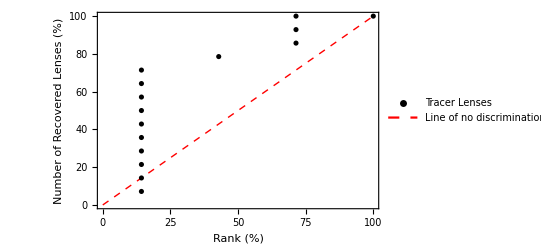

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.471088

| i | | | Tracer Lens Image | | | Name | | |             Class Probabilities             | | | Relative Rank in 7 | | | Rank in 235942) |
1 | -Graphics- | Lens 1 | {1.,6.90584×10^-10} | 0.142857 | 33706
2 | -Graphics- | Lens 11 | {1.,1.0946×10^-8} | 0.142857 | 33706
3 | -Graphics- | Lens 8 | {1.,7.73982×10^-13} | 0.142857 | 33706
4 | -Graphics- | Lens 16 | {1.,2.96519×10^-8} | 0.142857 | 33706
5 | -Graphics- | Lens 2 | {1.,3.09508×10^-14} | 0.142857 | 33706
6 | -Graphics- | Lens 6 | {1.,2.40774×10^-10} | 0.142857 | 33706
7 | -Graphics- | Lens 5 | {1.,1.60516×10^-7} | 0.142857 | 33706
8 | -Graphics- | Lens 4 | {0.999847,0.000153425} | 0.142857 | 33706
9 | -Graphics- | Lens 18 | {0.999831,0.000168544} | 0.142857 | 33706
10 | -Graphics- | Lens 7 | {0.079029,0.920971} | 0.142857 | 33706
11 | -Graphics- | Lens 3 | {0.000664327,0.999336} | 0.428571 | 101118
12 | -Graphics- | Lens 12 | {0.000306057,0.999694} | 0.714286 | 168530
13 | -Graphics- | Lens 9 | {0.0002221,0.999778} | 0.714286 | 168530
14 | -Graphics- | Lens 17 | {0.000111156,0.999889} | 0.714286 | 168530

```mathematica
sortedCosmos=sortedCosmos;
scannedKnownLenses1=scan[tracerLenses,trainedNetPhase1];
sortedKnownLenses1=sort[scannedKnownLenses1,{"lens"},classesPhase1];
relativeTracerRanks1=rankLocator[{"lens"},{#},sortedCosmos,classesPhase1][[1]]&/@sortedKnownLenses1[[All,3,1]]/(1.Length[sortedCosmos]);

efficiency[relativeTracerRanks1[[1;;-1]]]

rankPlot[relativeTracerRanks1]
rankingPerformance[relativeTracerRanks1]

Grid[{{"| i |","| Tracer Lens Image |","| Name |","|             Class Probabilities             |","| Relative Rank in "<>ToString@Length[sortedCosmos]<>" |","| Rank in 235942) |"}}~Join~Table[Join[{i},sortedKnownLenses1[[i]],{relativeTracerRanks1[[i]],Ceiling[235942relativeTracerRanks1[[i]]]}],{i,Length[sortedKnownLenses1]}]]
```

Select top candidates from cosmos.

```mathematica
cosmosPhase2=sortedCosmos[[1;;7(*14000*)]];
```

## Phase 2

Fine Classification Phase. See Section 3.5 of the paper. Now we will be using the remaining cosmos images to retrain the network and use it to re-rank the remaining images. We will also employ “boot strapping”.

### Creating Datasets

Here, I use a technique which I call "bootstrapping". After retraining our CNN on the remainder of cosmos (i.e. cosmosPhase2), we can take top ranked false positives such as spiral galaxies, satellite  galaxies, stars, artifacts, etc. and add them to our training dataset to improve the performance of our neural net. This has been made very easy thanks to the “view” function. Simply view the top few hundred sorted images, eliminate lenses, use the rest (called other) to augment and to rotate them, and add them to the training dataset.

```mathematica
other={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
other//Length
```

10

```mathematica
{trainingDataPhase2,testDataPhase2}=Join[
datasetMaker[simulatedLenses,"lens",0,0,95{1,1},True,imageSize],
datasetMaker[simulatedLenses,"lens",0,8,95{1,1},False,imageSize],
(*Only use the 2000 random cosmosPhase2 images*)
datasetMaker[RandomSample[cosmosPhase2[[All,1]],5(*2000*)],"non-lens",0,0,95{1,1},False,imageSize],

datasetMaker[other,"non-lens",0,0,95{1,1},True,imageSize],
datasetMaker[other,"non-lens",0,8,95{1,1},False,imageSize],
2];
```

### Net Setup

```mathematica
classesPhase2={"lens","non-lens"};
netPhase2=NetChain[trainedNetCIFAR2[[All]],"Output"->NetDecoder[{"Class",classesPhase2}],
"Input"->NetEncoder[{"Image",ColorSpace->"Grayscale",imageSize }]];
```

### Training

```mathematica
trainedNetPhase2=NetTrain[netPhase2,trainingDataPhase2,MaxTrainingRounds->25,Method->{"ADAM","LearningRate"->0.0005},TargetDevice->targetDevice,LearningRateMultipliers->{11->1,12->1,13->1,14->1,15->1,16->1,17->1,18->1,19->1,20->1,21->1,_->.1}]
```

NetChain[<>]

### Net Assessment

Keep in mind that the full dataset has not been included in this notebook and that’s why the plots and the tables bellow might not make a lot of sense.

#### Scanning and Sorting Cosmos Data (the remaining)

```mathematica
scannedCosmosPhase2=scan[cosmosPhase2[[1;;-1]],trainedNetPhase2];
sortedCosmosPhase2=sort[scannedCosmosPhase2,{"lens"},classesPhase2];
```

#### Scanning and Sorting Tracer Lenses

0.714286

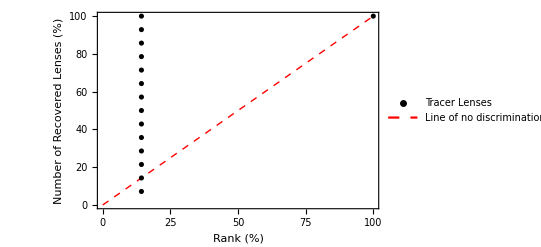

| i | | | Tracer Lens Image | | | Name | | |             Class Probabilities             | | | Relative Rank in 7 | | | Rank in 7) |
1 | -Graphics- | Lens 7 | {0.999116,0.000883529} | 0.142857 | 1
2 | -Graphics- | Lens 5 | {0.998658,0.00134166} | 0.142857 | 1
3 | -Graphics- | Lens 9 | {0.998602,0.00139838} | 0.142857 | 1
4 | -Graphics- | Lens 12 | {0.997634,0.0023663} | 0.142857 | 1
5 | -Graphics- | Lens 11 | {0.995518,0.00448184} | 0.142857 | 1
6 | -Graphics- | Lens 18 | {0.994274,0.00572575} | 0.142857 | 1
7 | -Graphics- | Lens 16 | {0.993801,0.00619935} | 0.142857 | 1
8 | -Graphics- | Lens 1 | {0.992656,0.00734429} | 0.142857 | 1
9 | -Graphics- | Lens 17 | {0.98946,0.0105396} | 0.142857 | 1
10 | -Graphics- | Lens 4 | {0.988226,0.0117745} | 0.142857 | 1
11 | -Graphics- | Lens 6 | {0.983234,0.0167657} | 0.142857 | 1
12 | -Graphics- | Lens 2 | {0.982658,0.0173417} | 0.142857 | 1
13 | -Graphics- | Lens 8 | {0.914614,0.0853859} | 0.142857 | 1
14 | -Graphics- | Lens 3 | {0.904469,0.0955309} | 0.142857 | 1

```mathematica
scannedKnownLenses2=scan[tracerLenses,trainedNetLens];
sortedKnownLenses2=sort[scannedKnownLenses2,{"lens"},classesPhase2]
relativeTracerRanks2=rankLocator[{"lens"},{#},sortedCosmosPhase2,classesPhase2][[1]]&/@sortedKnownLenses2[[All,3,1]]/(1.Length[sortedCosmosPhase2]);

efficiency[relativeTracerRanks2[[1;;-1]]]
rankPlot[relativeTracerRanks2]

Grid[{{"| i |","| Tracer Lens Image |","| Name |","|             Class Probabilities             |","| Relative Rank in "<>ToString@Length[sortedCosmosPhase2]<>" |","| Rank in "<>ToString[Length[sortedCosmosPhase2]]<>") |"}}~Join~Table[Join[{i},sortedKnownLenses2[[i]],{relativeTracerRanks2[[i]],Ceiling[Length[sortedCosmosPhase2]relativeTracerRanks2[[i]]]}],{i,Length[sortedKnownLenses2]}]]
```

```mathematica
view[sortedCosmosPhase2,1,2,3]
```

-Graphics-
1 | -Graphics-
2 | -Graphics-
3
-Graphics-
4 | -Graphics-
5 | -Graphics-
6

## Lens Discovery Phase (Phase 3)

Visually exam the high ranking images using “view”.

```mathematica
view[sortedCosmosPhase2,1,2,3]
```

-Graphics-
1 | -Graphics-
2 | -Graphics-
3
-Graphics-
4 | -Graphics-
5 | -Graphics-
6

Find file name for image number 2:

```mathematica
sortedCosmosPhase2[[2]]
```

{-Graphics-,enh_cosmos_acs_t078_i1011_x8965_y4121.jpeg,{0.0730518,0.926948}}

## Plots and Performance

Here, you can generate some useful plot. The data used here has been reduced for transparency and are not identical to the plots you see in our paper.

### Image Histogram

```mathematica
templateHistogram=HistogramDistribution@ImageAdjust[-Graphics-,{1.,.5,.3}];
```

```mathematica
epilogImage=ImageAdjust[-Graphics-,{1.,.5,.3}]
```

-Graphics-

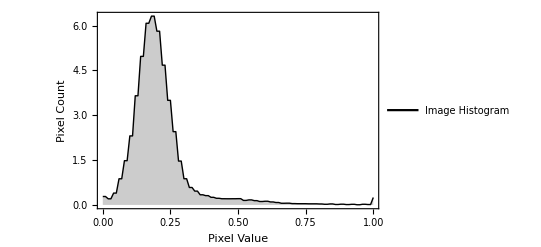

```mathematica
imageHistoPlot=ListPlot[
{Table[{i,PDF[templateHistogram,i]},{i,0,1,.01}]},
(*PlotRange->{Automatic},*)
Joined->{True},
PlotStyle->{Directive[Black,Thick]},
Filling->Axis,
PlotLegends->Placed[{"Image Histogram"},{Scaled[{0.58,0.15}], {0., 0.5}}],
Frame->True,
FrameLabel->{"Pixel Value","Pixel Count"},
FrameStyle->Directive[Black,12],
Epilog->{Inset[epilogImage,Scaled[{.2+0.58,0.2+.4}],Automatic,.4]}
]
```

### Tabulated Layers

```mathematica
TraditionalForm[netCIFAR2]
```

| input | image
3-tensor (size: ××1100100)
1 | convolution | 3-tensor (size: ××309696)
2 | tanh | 3-tensor (size: ××309696)
3 | pooling | 3-tensor (size: ××304848)
4 | convolution | 3-tensor (size: ××604444)
5 | tanh | 3-tensor (size: ××604444)
6 | pooling | 3-tensor (size: ××602222)
7 | convolution | 3-tensor (size: ××901818)
8 | tanh | 3-tensor (size: ××901818)
9 | pooling | 3-tensor (size: ××9099)
10 | flatten | vector (size: ××7290)
11 | linear | vector (size: ××1000)
12 | ReLU | vector (size: ××1000)
13 | dropout | vector (size: ××1000)
14 | linear | vector (size: ××800)
15 | ReLU | vector (size: ××800)
16 | dropout | vector (size: ××800)
17 | linear | vector (size: ××600)
18 | ReLU | vector (size: ××600)
19 | dropout | vector (size: ××600)
20 | linear | vector (size: ××2)
21 | softmax | vector (size: ××2)
 | output | class

### Ranks

#### Plot Tracer Rank Curve and Calculate Ranking Perfromance

Example of relative tracer ranks from Phase2:

```mathematica
relativeTracerRanks2={0.00817647,0.0156471,0.0214706,0.0237647,0.0262941,0.0289412,0.0336471,0.0341176,0.0364118,0.0417647,0.047,0.0548235,0.0554118,0.0575882,0.0610588,0.0617059,0.0618824,0.0657647,0.0727059,0.0757647,0.0967059,0.111176,0.117588,0.132882,0.134765,0.141412,0.147588,0.152176,0.168706,0.183471,0.209118,0.226765,0.23,0.237176,0.243647,0.250765,0.261706,0.262118,0.278765,0.290529,0.300412,0.304471,0.324882,0.357706,0.389,0.411706,0.453765,0.477412,0.649647,0.729059,0.859118,0.934118};
```

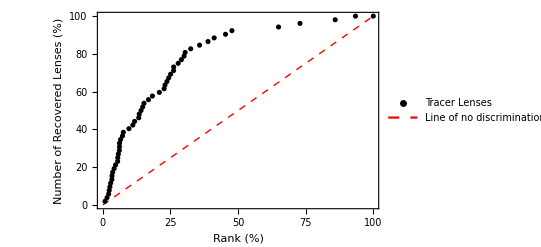

```mathematica
rankPlotPhase2=rankPlot[relativeTracerRanks2]
```

This gives you the area between the black line and the dashed curves line divided by the area of the upper triangle:

```mathematica
rankingPerformance[relativeTracerRanks2]
```

InterpolatingFunction::dmvali: The integration endpoint 0 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

0.596667

### ROC Curve

#### Creating Datasets

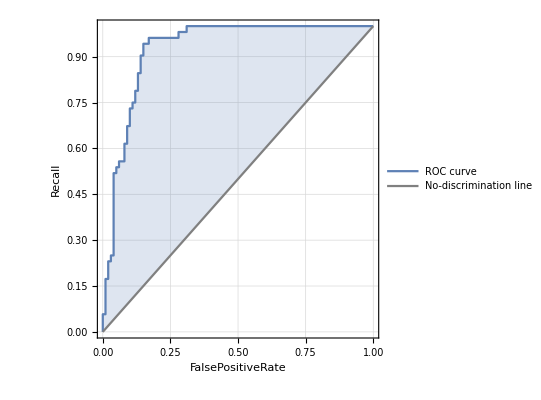
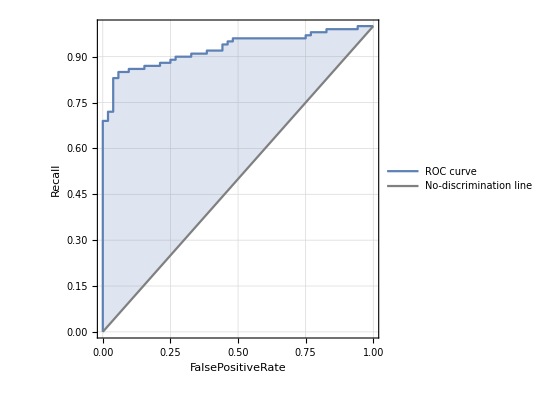
<|lens→-Graphics-,non-lens→-Graphics-|>

```mathematica
trainedNetROC=trainedNetPhase2;
{testDataROC,ignore}=Join[
datasetMaker[tracerLenses[[All,1]],"lens",0,a,95{1,1},True,imageSize],
datasetMaker[tracerLenses[[All,1]],"lens",0,8,95{1,1},False,imageSize],

datasetMaker[other,"non-lens",0,a,95{1,1},True,imageSize],
datasetMaker[other,"non-lens",0,8,95{1,1},False,imageSize],
2];
ROC=ClassifierMeasurements[trainedNetROC,testDataROC,"ROCCurve"]
```

Extract the point coords from the plot above. I am dropping {0, 0} and {1, 1} by selecting [[2;;-4]].

```mathematica
ROCdata1=ROC[[1,1,1,2,1]][[2;;-4]];
```

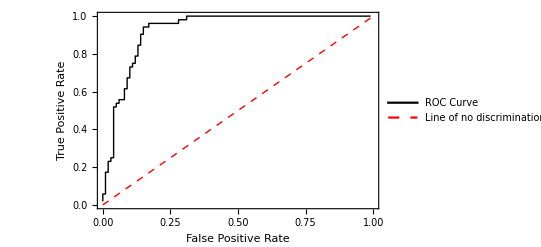

```mathematica
ROCCurve=ListPlot[
{ROCdata1,Table[{i,i},{i,0,1,.1}]},
PlotRange->{All,All},
Joined->{True,True},
PlotStyle->{Directive[Black,Thick],Directive[Red,Thin,Dashed]},

PlotLegends->Placed[{"ROC Curve","Line of no discrimination"},{Scaled[{0.38,0.15}], {0., 0.5}}],
Frame->True,
FrameLabel->{"False Positive Rate","True Positive Rate"},
FrameStyle->Directive[Black,12]]
```